# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\Spectrum of E

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Spectrum of ϵ

```mathematica
L=3;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
L=3;
ψe=RandomChainProductState[L-1];
```

```mathematica
tf=50.;
dt=0.01;
tlist=Range[0,tf,dt];
hzlist=Range[0,4,0.1];
hx=J=1.;
colorRange=ColorData["BlueGreenYellow"][#]&/@Rescale[Range[0,1,1/Length[hzlist]],{0,1},{0,1}];
```

```mathematica
plots1={};
plots2={};
plots3={};
plots4={};
Do[

H=IsingNNOpenHamiltonian[hx,hzlist[[i]],J,L];
(*H=ClosedXXZHamiltonian[L,hzlist[[i]]];*)
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
data1={};
data2={};
Do[
superOp=Superoperator[t,ψe,eigenval,eigenvec,L];(*AppendTo[choiEigenvalues,Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];*)
AppendTo[data1,Transpose[Sort[Transpose[Eigensystem[superOp]]]]];
(*AppendTo[data2,Reshuffle[(1/2)superOp]];*)
,{t,0,tf,dt}];
eigenvalues=Table[data1[[i,1]],{i,Length[data1]}];
uno=ComplexListPlot[eigenvalues,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,PlotTheme->"Detailed",PlotStyle->colorRange[[i]],ImageSize->1000,PlotLabel->Style["Wisniacki chain, L = "<>ToString[L]<>", tf = "<>ToString[tf]<>", hz = "<>ToString[hzlist[[i]]],25,Black],Frame->True];
dos=ListPlot[Table[{tlist[[i]],Chop[Total[eigenvalues[[i]]]]},{i,Length[eigenvalues]}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->colorRange[[i]],ImageSize->1000,PlotLabel->Style["Wisniacki chain, L = "<>ToString[L]<>", tf = "<>ToString[tf]<>", hz = "<>ToString[hzlist[[i]]],25,Black]];
tres=ListPlot[Table[{tlist[[i]],Chop[Times@@eigenvalues[[i]]]},{i,Length[eigenvalues]}],PlotRange->All,PlotTheme->"Detailed",PlotStyle->colorRange[[i]],ImageSize->1000,PlotLabel->Style["Wisniacki chain, L = "<>ToString[L]<>", tf = "<>ToString[tf]<>", hz = "<>ToString[hzlist[[i]]],25,Black]];
cuatro=ListPlot[Transpose[Abs[eigenvalues]],PlotRange->All,PlotTheme->"Detailed",PlotStyle->colorRange[[i]],ImageSize->1000,PlotLabel->Style["Wisniacki chain, L = "<>ToString[L]<>", tf = "<>ToString[tf]<>", hz = "<>ToString[hzlist[[i]]],25,Black]];

AppendTo[plots1,uno];
AppendTo[plots2,dos];
AppendTo[plots3,tres];
AppendTo[plots4,cuatro];

,{i,Length[hzlist]}];
```

$Aborted

```mathematica
ListAnimate[plots1,AnimationRunning->False]
```

```mathematica
ListAnimate[plots2,AnimationRunning->False]
```

```mathematica
ListAnimate[plots3,AnimationRunning->False]
```

```mathematica
ListAnimate[plots4,AnimationRunning->False]
```

```mathematica
Export["ListPlotMovie_abseigenval_tf_"<>ToString[tf]<>".mp4",plots4,"FrameRate"->2]
```

ListPlotMovie_abseigenval_tf_0.5.mp4

```mathematica
Export["ListPlotMovie_spectrum_tf_"<>ToString[tf]<>".mp4",plots1,"FrameRate"->1]
Export["ListPlotMovie_trace_tf_"<>ToString[tf]<>".mp4",plots2,"FrameRate"->1]
Export["ListPlotMovie_det_tf_"<>ToString[tf]<>".mp4",plots3,"FrameRate"->1]
Export["ListPlotMovie_abseigenval_tf_"<>ToString[tf]<>".mp4",plots4,"FrameRate"->1]
(*Export["ListPlotMovie_xxz_spectrum_tf_"<>ToString[tf]<>".mp4",plots1,"FrameRate"->2]
Export["ListPlotMovie_xxz_trace_tf_"<>ToString[tf]<>".mp4",plots2,"FrameRate"->2]
Export["ListPlotMovie_xxz_det_tf_"<>ToString[tf]<>".mp4",plots3,"FrameRate"->2]
Export["ListPlotMovie_xxz_abseigenval_tf_"<>ToString[tf]<>".mp4",plots4,"FrameRate"->2]*)
```

ListPlotMovie_spectrum_tf_50..mp4

ListPlotMovie_trace_tf_50..mp4

ListPlotMovie_det_tf_50..mp4

ListPlotMovie_abseigenval_tf_50..mp4

```mathematica
data2//Dimensions
```

{201,4,4}

```mathematica
{choival,choivec}=Transpose[Sort[Transpose[Eigensystem[data2[[-1]]]]]];
```

```mathematica
Times@@choival
```

0.000158235

```mathematica
data2[[-1]]//MatrixForm
```

(0.271339+0. ⅈ | 0.0792025-0.0912694 ⅈ | -0.00818936+0.0104644 ⅈ | -0.0125496-0.163455 ⅈ
0.0792025+0.0912694 ⅈ | 0.186086+0. ⅈ | -0.0739705+0.0568215 ⅈ | 0.161904-0.0654725 ⅈ
-0.00818936-0.0104644 ⅈ | -0.0739705-0.0568215 ⅈ | 0.228661+0. ⅈ | -0.0792025+0.0912694 ⅈ
-0.0125496+0.163455 ⅈ | 0.161904+0.0654725 ⅈ | -0.0792025-0.0912694 ⅈ | 0.313914+0. ⅈ)

```mathematica
Chop[Tr[data2[[-1]]]]
```

1.

```mathematica
hzlist=Range[0,4,0.01];
```

```mathematica
eigenvalues=Table[Table[{hzlist[[i]],j},{j,Sort[Eigenvalues[IsingNNOpenHamiltonian[hx,hzlist[[i]],J,3]]]}],{i,Length[hzlist]}];
```

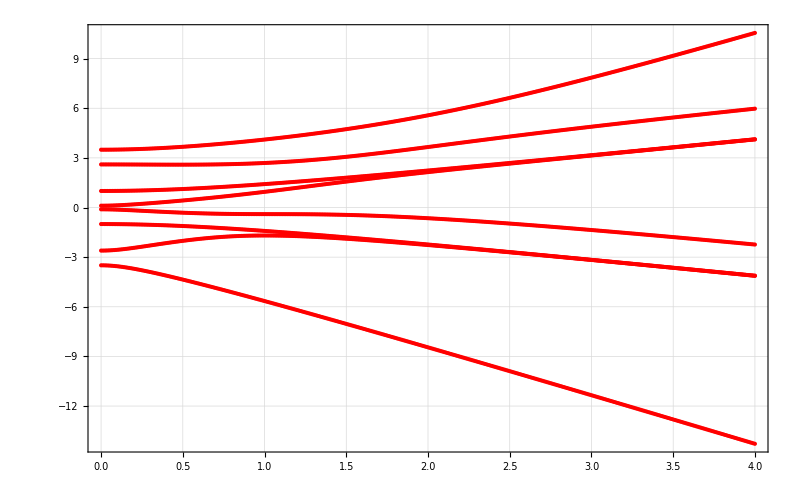

```mathematica
ListPlot[eigenvalues,PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",ImageSize->800]
```

```mathematica
L=3;
ψe=RandomChainProductState[L-1];
```

```mathematica
tf=10.;
tlist=Range[0,tf,0.1];
hzlist=Range[0,0.5,0.1];
colorRange=ColorData["BlueGreenYellow"][#]&/@Rescale[Range[0,1,1/Length[hzlist]],{0,1},{0,1}];
```

```mathematica
hx=J=1.;
```

```mathematica
H=IsingNNOpenHamiltonian[hx,0.5,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
t=0.1;
superOp=Superoperator[t,ψe,eigenval,eigenvec,L];
{eigenvala,eigenveca}=Transpose[Sort[Transpose[Eigensystem[superOp]]]];
```

```mathematica
caometer=haar[1];
caometermatrix=Dyad[caometer];
```

```mathematica
caometervec={caometermatrix[[1,1]],caometermatrix[[1,2]],caometermatrix[[2,1]],caometermatrix[[2,2]]};
```

```mathematica
newcaometer=superOp.caometervec;
```

```mathematica
Chop[Purity[ArrayReshape[newcaometer,{2,2}]]]
```

0.99166

```mathematica
newnewcaometer=ConjugateTranspose[caometer].ArrayReshape[ConjugateTranspose[superOp].superOp.caometervec,{2,2}].caometer//Chop
```

0.99166

# SSF(t)

Let’s consider the SP(t) of random product states and their average

```mathematica
hzlist=Range[0,4,0.01];
```

```mathematica
L=3;
hx=J=1;
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[IsingNNOpenHamiltonian[hx,0.5,J,3]]]]];
```

```mathematica
ale=100;
random=Table[RandomChainProductState[L],{i,ale}];
```

```mathematica
eigenrandom=ParallelTable[Conjugate[eigenvec].i,{i,random}];
```

```mathematica
Clear[sp];
sp[state_,t_]:=Abs[Total[Table[(Exp[-I*eigenval[[i]]*t])Abs[state[[i]]]^2,{i,Length[state]}]]]^2;
```

```mathematica
tlist=Range[0,1000,0.01];
```

```mathematica
data=ParallelTable[Table[{t,sp[j,t]},{t,tlist}],{j,eigenrandom}];
```

```mathematica
plots=ListLogLogPlot[data[[1;;-1;;10]],PlotRange->{All,{10^-1.8,1}},PlotTheme->"Detailed",Joined->True,PlotStyle->{Directive[Gray,Opacity[0.2]]},ImageSize->600];
```

```mathematica
meanplots=ListLogLogPlot[Mean[data],PlotRange->{All,{10^-1.8,1}},PlotTheme->"Detailed",Joined->True,PlotStyle->{Directive[Black,Opacity[0.6]]},ImageSize->600];
```

```mathematica
Export["sff.png",Show[{meanplots,plots}],ImageSize->1000]
```

sff.png